# TuGamesView3dV6

A basic Introduction

by Holger I.Meinhardt, University of Karlsruhe (KIT)

## General Remarks

In order to depict game solutions for four person games only at least three packages must be loaded. Firstly, we need to load the package "CooperativeGames`" written by M. Carter to provide some basic functions, then the package "TuGames`" and finally "IOTuGamesV6`". The last package provides all functions to plot three dimensional game solutions. This package is an upgrade of the package "IOTuGames`" to keep track with the new graphic concept of Mathematica version 6. x and higher. To use the old graphic concept of Mathematica version 5. x and lower one has to load the old package "IOTuGames`" in connection with << Version5`Graphics`. The last command restores the old graphic concept of Mathematica. For a proper functionality, it is important to note that one cannot mix in one notebook both graphic concepts. One has to made a decision which graphic concept should be used.  Moreover, the notebook of Mathematica 5.x cannot handle graphic objects generated by Mathematica 6.x and higher, in this case Mathematica 5.x will probably crash.  All graphical extensions require the cddmathlink libraries by Komei Fukuda and  his package <<PolytopeSkeleton.m. In this respect notice that the cddmathlink libraries can be compiled for all platforms, we expect, therefore, that the graphical extensions should now be usable under all platforms in contrast to the old package which provides its graphical functionality only for UNIX system. For more details see the section requirements in the IOTuGamesV6.m file.

## Getting Started

If everything is installed properly, we can now load the above mentioned packages while typing

```mathematica
Needs["TUG`"];
```

===================================================

Loading Package 'TuGames' for Unix

===================================================

TuGames V3.1.4 by Holger I. Meinhardt

Release Date: 31.05.2024

Program runs under Mathematica Version 12.0 or later

Version 12.x or higher is recommended

===================================================

===================================================

Package 'TuGames' loaded

===================================================

For loading the cddmathlink libraries the directory is internally set to the directory where the cddmathlink libraries are installed, to restore the original path from which Mathematica was started we reset the directory by

```mathematica
(* ResetDirectory[]; *)
```

This is required when one has the intention to export some of the generated graphics and to find them again in the current working directory. Otherwise, the exported graphics are copied to the installation directory of the cddmathlink libraries, which would be in this case the current working directory.

A list of functions, options and variables available by the Mathematica package IOTuGamesV6.m are given while invoking

```mathematica
?TUG`IOTuGamesV6`*
```

There are four basic user interfaces to depict the core, the strong epsilon core, kernel catchers, and for animating the geometric property of the kernel, which are called PlotCore3dV6[], StrongEpsCore3dV6[], ShowKernelCatcherV6[], and AnimationKernelPropertyV6[],  respectively. In sequel we concentrate our discussion on these four graphic commands. Moreover, users who have already some experience with our old graphic package should be aware that the behavior of these functions is different w.r.t. the old functions. Due to the fact that the graphical and mathematical functionality of Mathematica has increased, we need just to call the mentioned functions with at most two arguments, the game name and a set of options. A graphic will be plotted if the semicolon is omitted, otherwise the graphic will be suppressed. To find out more about a function, option or variable, one has just to click on the command name to get some basic information how to use it.

Now we are in the position to define a four person example game, which is done by providing the player set T, and the valuation of the coalitions, which is given by a vector of coalition values. These information are sufficient to specify a transferable utility game. This is done by determining the 16 components of the list "clv", and the four player set given by the variable T. The function that defines the game for us is called DefineGame[]. By default this function defines the game in rational numbers rather than by floating point numbers. In order to get a game definition in floating point numbers the option "RationalApproximate" must be set to "False".

```mathematica
clv={0,0,0,0,0.54839,0,0,15.67188,0,13.54167,11.55263,0,40.75862,36.47619,32.63158,96.29412};
```

```mathematica
T={1,2,3,4};
```

```mathematica
ExpGame11=DefineGame[T,clv];
```

To test that the game has been defined properly, we verify first whether the game is convex.

```mathematica
ConvexQ[ExpGame11]
```

True

Everything seems to be fine. In the next step we compute the Shapley value, the kernel solution, and the nucleolus to visualize how these solutions are related to the core, the strong epsilon core, and kernel catchers. Notice that we need not compute these solution concepts in advance to visualize them later in a three dimensional plot. It is just enough to set the corresponding option to "True" and let the coordinate list empty when calling one of the above plot commands, since every time one of these plot functions is called for, these solutions will be computed from scratch whenever these lists are empty, otherwise the computation is suppressed.

```mathematica
ker=Kernel[ExpGame11]
```

{2214694385/92523996,2214694385/92523996,2214694385/92523996,2265433619/92523996}

```mathematica
shv=ShapleyValue[ExpGame11]
```

{551664375656423187653/25633808250918480000,101942562274892938093/5126761650183696000,2323116849340671928481/128169041254592400000,4711922254770259280929/128169041254592400000}

```mathematica
mnuc=ModifiedNucleolus[ExpGame11]
```

{2214694385/92523996,2214694385/92523996,2214694385/92523996,2265433619/92523996}

```mathematica
mnc=Modiclus[ExpGame11]
```

{402565090335976207/21615124334625000,178260168189514181/10807562167312500,156763494677801681/10807562167312500,1008796960491954569/21615124334625000}

The epsilon value of the least core is obtained from the following commands.

```mathematica
First[EpsCore[ExpGame11]]//N
```

-23.9364

```mathematica
FirstCriticalVal[ExpGame11]//N
```

{eps1→-23.9364}

These are the basic information needed to follow the instructions how to use the graphical extension of the Mathematica package "TuGames`". In the sequel we show how different graphic types can be plotted, and which options can be invoked in connection with a graphic command for fading in or out additional solution concepts.

## Core Plot3d

```mathematica
Options[PlotCore3dV6]
```

{HarsanyiValCoord→{},KernelCoord→{},ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowImputationSet→True,ShowWeberSet→False,SyncDim→True,Verbosely→True,ViewHarsanyiSol→False,ViewKernelSol→False,ViewLegend→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False,VRepresentation→False}

```mathematica
gr0=PlotCore3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{},Boxed->True]
```

-Graphics3D-

```mathematica
gr1=PlotCore3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
gr2=PlotCore3dV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
gr3=PlotCore3dV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
gr4=PlotCore3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

-Graphics3D-

```mathematica
gr5=PlotCore3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

-Graphics3D-

```mathematica
gr6=PlotCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
gr7=PlotCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
gr8=PlotCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

-Graphics3D-

```mathematica
gr9=PlotCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

-Graphics3D-

```mathematica
gr10=PlotCore3dV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},Boxed->True]
```

-Graphics3D-

```mathematica
gr11=PlotCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},Boxed->True]
```

-Graphics3D-

```mathematica
gr12=PlotCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,Boxed->True]
```

-Graphics3D-

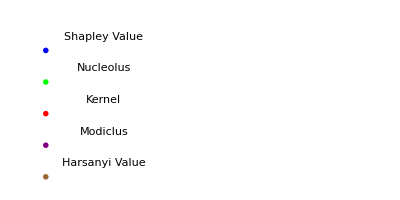

```mathematica
gr13=PlotCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,Boxed->True,ViewLegend-> True]
```

## Strong Epsilon Core

```mathematica
Options[StrongEpsCore3dV6]
```

{CriticalValue→{1},EpsStrValues→{},KernelCoord→{},ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowCore→True,ShowImputationSet→True,ShowStrongEpsCore→True,SyncDim→True,ViewKernelSol→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False}

```mathematica
g0=StrongEpsCore3dV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,Boxed->True]
```

-Graphics3D-

```mathematica
g1=StrongEpsCore3dV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker]
```

-Graphics3D-

```mathematica
g2=StrongEpsCore3dV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,EpsStrValues->15]
```

-Graphics3D-

```mathematica
g3=StrongEpsCore3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc,EpsStrValues->25]
```

-Graphics3D-

```mathematica
g4=StrongEpsCore3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->True,NucleolusCoord->mnuc,EpsStrValues->7]
```

-Graphics3D-

```mathematica
g5=StrongEpsCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},EpsStrValues->-4]
```

-Graphics3D-

```mathematica
g6=StrongEpsCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},EpsStrValues->10]
```

-Graphics3D-

```mathematica
g7=StrongEpsCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc,EpsStrValues->-10]
```

-Graphics3D-

```mathematica
g8=StrongEpsCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->True,NucleolusCoord->mnuc,EpsStrValues->18]
```

-Graphics3D-

```mathematica
g9=StrongEpsCore3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{},EpsStrValues->-5]
```

-Graphics3D-

```mathematica
g10=StrongEpsCore3dV6[ExpGame11,ViewSkel->False,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{},EpsStrValues->-5]
```

-Graphics3D-

```mathematica
g11=StrongEpsCore3dV6[ExpGame11,ViewSkel->False,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{},EpsStrValues->-20]
```

-Graphics3D-

```mathematica
g12=StrongEpsCore3dV6[ExpGame11,ViewSkel->False,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->True,NucleolusCoord->{},EpsStrValues->-20]
```

-Graphics3D-

```mathematica
g13=StrongEpsCore3dV6[ExpGame11,ViewSkel->False,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},EpsStrValues->-20]
```

-Graphics3D-

## Weber Set Plot3d

Recall that for convex games the Weber set coincides with the core. The Weber set is drawn as an orange polytope.

```mathematica
Options[PlotWeberSet3dV6]
```

{HarsanyiValCoord→{},KernelCoord→{},ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowImputationSet→True,SyncDim→True,Verbosely→True,ViewHarsanyiSol→False,ViewKernelSol→False,ViewLegend→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False,VRepresentation→False}

```mathematica
wb0=PlotWeberSet3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{},Boxed->True]
```

-Graphics3D-

```mathematica
wb1=PlotWeberSet3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
wb2=PlotWeberSet3dV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
wb3=PlotWeberSet3dV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
wb4=PlotWeberSet3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

-Graphics3D-

```mathematica
wb5=PlotWeberSet3dV6[ExpGame11,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

-Graphics3D-

```mathematica
wb6=PlotWeberSet3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
wb7=PlotWeberSet3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

-Graphics3D-

```mathematica
wb8=PlotWeberSet3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

-Graphics3D-

```mathematica
wb9=PlotWeberSet3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->False,ShapleyCoord->{},ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

-Graphics3D-

```mathematica
wb10=PlotWeberSet3dV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},Boxed->True]
```

-Graphics3D-

```mathematica
wb11=PlotWeberSet3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},Boxed->True]
```

-Graphics3D-

```mathematica
wb12=PlotWeberSet3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,Boxed->True]
```

-Graphics3D-

```mathematica
wb13=PlotWeberSet3dV6[ExpGame11,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},ViewModiclusSol->True,ModiclusCoord->mnc,Boxed->True,ViewLegend-> True]
```

-Graphics-

## Kernel Catchers

```mathematica
Options[ShowKernelCatcherV6]
```

{CriticalValue→{1},EpsStrValues→{},KernelCoord→{},ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowCore→False,ShowImputationSet→True,ShowLowerSet→False,ShowStrongEpsCore→False,ShowUpperSet→True,SyncDim→True,ViewKernelSol→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False}

```mathematica
k1=ShowKernelCatcherV6[ExpGame11,ShowLowerSet->True,ShowUpperSet->True]
```

-Graphics3D-

```mathematica
k2=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->False,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k3=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->False,ShowStrongEpsCore->True,EpsStrValues->{},ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k4=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->False,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->20,ViewSkel->True,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k5=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->False,ShowStrongEpsCore->True,EpsStrValues->20,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k6=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->20,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k7=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->-20,ViewSkel->True,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k8=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->-10,ViewSkel->False,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k9=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->-20,ViewSkel->False,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k10=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->20,ViewSkel->False,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k11=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->False,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->20,ViewSkel->False,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k12=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->False,ShowStrongEpsCore->True,EpsStrValues->20,ViewSkel->False,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k13=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->False,ShowUpperSet->False,ShowStrongEpsCore->True,EpsStrValues->20,ViewSkel->False,ViewKernelSol->False,KernelCoord->{},ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->True,NucleolusCoord->mnuc]
```

Is core nonempty? True

-Graphics3D-

```mathematica
k14=ShowKernelCatcherV6[ExpGame11,ShowCore->True,ShowLowerSet->True,ShowUpperSet->True,ShowStrongEpsCore->True,EpsStrValues->15,ViewSkel->False,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{}]
```

Is core nonempty? True

-Graphics3D-

## Animate Geometric Property of the Kernel/Nucleolus

After we have learned how to depict three dimensional game solutions, a few words are in order to understand how to use the animation command to visualize the geometric property of the kernel/nucleolus. The function AnimationKernelPropertyV6[] generates in a first step a list of frames which can later on be rendered by the front-end of Mathematica having the side-effect that the frames can be exported much more easier than relying on the Mathematica built-in command Animate[] or Manipulate[]. While calling AnimationKernelPropertyV6[] with a semicolon the rendering process of the front-end is suppressed, only the graphical primitives have been produced. This is done to get some of the old graphical behavior back to run more smoothly an animation, this is due that all frames are produced from the beginning, and nothing must be recalculated from scratch. But before we discuss this behavior in more detail, we want discuss some crucial options, and with which values they can be invoked. Information about the set of options can be attained with the command

```mathematica
Options[AnimationKernelPropertyV6]
```

{CriticalValue→{1},EpsStrValues→{},KernelCoord→{},LowerCriticalVal→{},ManipulateMode→False,ModiclusCoord→{},NucleolusCoord→{},PayoffCoord→{},PictureSize→{400,434},PtRadius→0.021,ShapleyCoord→{},ShowCore→True,ShowImputationSet→True,ShowStrongEpsCore→True,StepSize→{-1/4},SyncDim→True,UpperCriticalVal→{1/2},ViewKernelSol→False,ViewModiclusSol→False,ViewNucleolusSol→False,ViewPayoffSol→False,ViewShapleySol→False,ViewSkel→False}

In the course of our discussion we want to plot the Shapley value and the kernel in connection with the core, imputation set, and strong epsilon core. For this reason the option "ViewNucleolusSol" is set to "False" due to the convexity of the game. However, the new options deserve some discussion. First there is the option "UpperCriticalVal" that specifies the largest strong epsilon core we want to consider, in this example the value is set to "25", its default value is 1/2. In contrast, the option "LowerCriticalVal" specifies the smallest strong epsilon core we want to depict. We notice that this value is unset or empty indicating that the least core is used by default. Furthermore, the option "StepSize" determines the shrinking speed of the epsilon value. The coarser this value the more erratic the motion of movie. The option "CriticalValue" indicates by its value "1" that the least core should be used as the upper bound for running the animation, which has here no effect, and which also is its default value. Having an effect, the option "UpperCriticalVal" must be unset with the empty set "{}". Finally, setting the options "ShowImputationSet", and "ShowCore" to "True" means that we want also consider the imputation set and the core of the game in the animation.

```mathematica
{time1,a1}=AbsoluteTiming[AnimationKernelPropertyV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},UpperCriticalVal->{25},LowerCriticalVal->{},CriticalValue->{1},StepSize->{-(1/5)},ShowImputationSet->True,ShowCore->True]];
```

Invoking the animation command, we have generated in total 245 frames for the movie in about 6 seconds as can be seen next

```mathematica
Length[a1]
```

245

```mathematica
time1
```

3.90733

These frames allow us to produce a QuickTime movie of 10 seconds. In order to get a longer and smoother movie more frames must be produced, this can be done while increasing the SepSize for instance from (-1/5) to (-1/20). How we can do that is postponed for while, first we want to demonstrate that with the variable a1 that grasp all frame information, we are able to run an animation while invoking the command

```mathematica
ListAnimate[a1,1]
```

Moreover, as we can seen next, the advantage of producing a list of frames allow us also to restore the old animation behavior of Mathematica 5. x and lower. For getting its old behavior back we have first to unravel the list in which the graphics are wrapped by Map[Print, a1]. This renders all 98 frames, selecting all the cells containing a graphic object and collapsing the cells let us allow to animate a movie within the notebook while selecting from the Menu the items Graphics -> Rendering -> Animate Selected Graphics.

```mathematica
Map[Print,a1];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«242 more identical outputs»

After having discussed these properties, we want come back to the question, how we can produce QuickTime movies. First export all frames in jpg - format by commenting out  the function below, which we have borrowed from Jens Noeckel

```mathematica
exportFrames[baseName_,a_,ext_:"jpg"]:=Module[{l=Length[a],d},d=Length@IntegerDigits[l];
Table[Export[baseName<>IntegerString[i,10,d]<>"."<>ext,Style[a[[i]],Magnification->1.5]],{i,l}]]
```

To speed up the procedure you can also use ParallelTable[] rather than Table[] if you have a multicore processor. Then invoke, for instance, exportFrames["Exp11krmovie", a1].

```mathematica
exportFrames["Exp11krmovie",a1]
```

{Exp11krmovie001.jpg,Exp11krmovie002.jpg,Exp11krmovie003.jpg,Exp11krmovie004.jpg,Exp11krmovie005.jpg,Exp11krmovie006.jpg,Exp11krmovie007.jpg,Exp11krmovie008.jpg,Exp11krmovie009.jpg,Exp11krmovie010.jpg,Exp11krmovie011.jpg,Exp11krmovie012.jpg,Exp11krmovie013.jpg,Exp11krmovie014.jpg,Exp11krmovie015.jpg,Exp11krmovie016.jpg,Exp11krmovie017.jpg,Exp11krmovie018.jpg,Exp11krmovie019.jpg,Exp11krmovie020.jpg,Exp11krmovie021.jpg,Exp11krmovie022.jpg,Exp11krmovie023.jpg,Exp11krmovie024.jpg,Exp11krmovie025.jpg,Exp11krmovie026.jpg,Exp11krmovie027.jpg,Exp11krmovie028.jpg,Exp11krmovie029.jpg,Exp11krmovie030.jpg,Exp11krmovie031.jpg,Exp11krmovie032.jpg,Exp11krmovie033.jpg,Exp11krmovie034.jpg,Exp11krmovie035.jpg,Exp11krmovie036.jpg,Exp11krmovie037.jpg,Exp11krmovie038.jpg,Exp11krmovie039.jpg,Exp11krmovie040.jpg,Exp11krmovie041.jpg,Exp11krmovie042.jpg,Exp11krmovie043.jpg,Exp11krmovie044.jpg,Exp11krmovie045.jpg,Exp11krmovie046.jpg,Exp11krmovie047.jpg,Exp11krmovie048.jpg,Exp11krmovie049.jpg,Exp11krmovie050.jpg,Exp11krmovie051.jpg,Exp11krmovie052.jpg,Exp11krmovie053.jpg,Exp11krmovie054.jpg,Exp11krmovie055.jpg,Exp11krmovie056.jpg,Exp11krmovie057.jpg,Exp11krmovie058.jpg,Exp11krmovie059.jpg,Exp11krmovie060.jpg,Exp11krmovie061.jpg,Exp11krmovie062.jpg,Exp11krmovie063.jpg,Exp11krmovie064.jpg,Exp11krmovie065.jpg,Exp11krmovie066.jpg,Exp11krmovie067.jpg,Exp11krmovie068.jpg,Exp11krmovie069.jpg,Exp11krmovie070.jpg,Exp11krmovie071.jpg,Exp11krmovie072.jpg,Exp11krmovie073.jpg,Exp11krmovie074.jpg,Exp11krmovie075.jpg,Exp11krmovie076.jpg,Exp11krmovie077.jpg,Exp11krmovie078.jpg,Exp11krmovie079.jpg,Exp11krmovie080.jpg,Exp11krmovie081.jpg,Exp11krmovie082.jpg,Exp11krmovie083.jpg,Exp11krmovie084.jpg,Exp11krmovie085.jpg,Exp11krmovie086.jpg,Exp11krmovie087.jpg,Exp11krmovie088.jpg,Exp11krmovie089.jpg,Exp11krmovie090.jpg,Exp11krmovie091.jpg,Exp11krmovie092.jpg,Exp11krmovie093.jpg,Exp11krmovie094.jpg,Exp11krmovie095.jpg,Exp11krmovie096.jpg,Exp11krmovie097.jpg,Exp11krmovie098.jpg,Exp11krmovie099.jpg,Exp11krmovie100.jpg,Exp11krmovie101.jpg,Exp11krmovie102.jpg,Exp11krmovie103.jpg,Exp11krmovie104.jpg,Exp11krmovie105.jpg,Exp11krmovie106.jpg,Exp11krmovie107.jpg,Exp11krmovie108.jpg,Exp11krmovie109.jpg,Exp11krmovie110.jpg,Exp11krmovie111.jpg,Exp11krmovie112.jpg,Exp11krmovie113.jpg,Exp11krmovie114.jpg,Exp11krmovie115.jpg,Exp11krmovie116.jpg,Exp11krmovie117.jpg,Exp11krmovie118.jpg,Exp11krmovie119.jpg,Exp11krmovie120.jpg,Exp11krmovie121.jpg,Exp11krmovie122.jpg,Exp11krmovie123.jpg,Exp11krmovie124.jpg,Exp11krmovie125.jpg,Exp11krmovie126.jpg,Exp11krmovie127.jpg,Exp11krmovie128.jpg,Exp11krmovie129.jpg,Exp11krmovie130.jpg,Exp11krmovie131.jpg,Exp11krmovie132.jpg,Exp11krmovie133.jpg,Exp11krmovie134.jpg,Exp11krmovie135.jpg,Exp11krmovie136.jpg,Exp11krmovie137.jpg,Exp11krmovie138.jpg,Exp11krmovie139.jpg,Exp11krmovie140.jpg,Exp11krmovie141.jpg,Exp11krmovie142.jpg,Exp11krmovie143.jpg,Exp11krmovie144.jpg,Exp11krmovie145.jpg,Exp11krmovie146.jpg,Exp11krmovie147.jpg,Exp11krmovie148.jpg,Exp11krmovie149.jpg,Exp11krmovie150.jpg,Exp11krmovie151.jpg,Exp11krmovie152.jpg,Exp11krmovie153.jpg,Exp11krmovie154.jpg,Exp11krmovie155.jpg,Exp11krmovie156.jpg,Exp11krmovie157.jpg,Exp11krmovie158.jpg,Exp11krmovie159.jpg,Exp11krmovie160.jpg,Exp11krmovie161.jpg,Exp11krmovie162.jpg,Exp11krmovie163.jpg,Exp11krmovie164.jpg,Exp11krmovie165.jpg,Exp11krmovie166.jpg,Exp11krmovie167.jpg,Exp11krmovie168.jpg,Exp11krmovie169.jpg,Exp11krmovie170.jpg,Exp11krmovie171.jpg,Exp11krmovie172.jpg,Exp11krmovie173.jpg,Exp11krmovie174.jpg,Exp11krmovie175.jpg,Exp11krmovie176.jpg,Exp11krmovie177.jpg,Exp11krmovie178.jpg,Exp11krmovie179.jpg,Exp11krmovie180.jpg,Exp11krmovie181.jpg,Exp11krmovie182.jpg,Exp11krmovie183.jpg,Exp11krmovie184.jpg,Exp11krmovie185.jpg,Exp11krmovie186.jpg,Exp11krmovie187.jpg,Exp11krmovie188.jpg,Exp11krmovie189.jpg,Exp11krmovie190.jpg,Exp11krmovie191.jpg,Exp11krmovie192.jpg,Exp11krmovie193.jpg,Exp11krmovie194.jpg,Exp11krmovie195.jpg,Exp11krmovie196.jpg,Exp11krmovie197.jpg,Exp11krmovie198.jpg,Exp11krmovie199.jpg,Exp11krmovie200.jpg,Exp11krmovie201.jpg,Exp11krmovie202.jpg,Exp11krmovie203.jpg,Exp11krmovie204.jpg,Exp11krmovie205.jpg,Exp11krmovie206.jpg,Exp11krmovie207.jpg,Exp11krmovie208.jpg,Exp11krmovie209.jpg,Exp11krmovie210.jpg,Exp11krmovie211.jpg,Exp11krmovie212.jpg,Exp11krmovie213.jpg,Exp11krmovie214.jpg,Exp11krmovie215.jpg,Exp11krmovie216.jpg,Exp11krmovie217.jpg,Exp11krmovie218.jpg,Exp11krmovie219.jpg,Exp11krmovie220.jpg,Exp11krmovie221.jpg,Exp11krmovie222.jpg,Exp11krmovie223.jpg,Exp11krmovie224.jpg,Exp11krmovie225.jpg,Exp11krmovie226.jpg,Exp11krmovie227.jpg,Exp11krmovie228.jpg,Exp11krmovie229.jpg,Exp11krmovie230.jpg,Exp11krmovie231.jpg,Exp11krmovie232.jpg,Exp11krmovie233.jpg,Exp11krmovie234.jpg,Exp11krmovie235.jpg,Exp11krmovie236.jpg,Exp11krmovie237.jpg,Exp11krmovie238.jpg,Exp11krmovie239.jpg,Exp11krmovie240.jpg,Exp11krmovie241.jpg,Exp11krmovie242.jpg,Exp11krmovie243.jpg,Exp11krmovie244.jpg,Exp11krmovie245.jpg}

Finally, from the command line of your operating system type, for instance, 
ffmpeg -i Exp11krmovie%02d.jpg -qscale 0 Exp11krmovie1.mp4

or alternatively

ffmpeg -framerate 25 -pattern_type glob -i ‘*.jpg’ -c:v libx264 -r 30 -pix_fmt yuv420p Exp11krmovie1.mp4

in case that you have less than 100 frames, however, up to 999 frames use 

ffmpeg -i Exp11krmovie%03d.jpg -qscale 0 Exp11krmovie1.mp4

or  alternatively

ffmpeg -framerate 25 -pattern_type glob -i ‘*.jpg’ -c:v libx264 -r 30 -pix_fmt yuv420p Exp11krmovie1.mp4

For additional information or for other movie formats consult the very nice website of Jens Noeckel, which is available under the URL
http : // pages.uoregon.edu/noeckel/MathematicaGraphics.html

The function AnimationKernelPropertyV6[] also allows us to generate an interactive graphic with the Manipulate[] command. For doing so, it is just enough to set the option "ManipulateMode" to "True", then it is possible to manipulate interactively the strong epsilon value and the viewpoint of the graphic. Notice that in this case, everything must be recomputed/re-rendered from scratch whenever you update the epsilon value with the slider or the control wrapper. Depending on your machine and graphic card this can result in a slow evaluation, and makes the use of this option more annoying rather than a real experience. To get some idea whether your machine lets expect an erratic motion you should check out the timing of the evaluation of the interactive graphic below. If the computation of the 3d-graphic needs far more than the 0.002 seconds as in our case, then one must expect an annoying behavior of the interactive manipulation. However, updating the viewpoint needs no reevaluation/re-rendering of the graphic producing a more harmonic motion. In addition, note that the variable a2 contains a dynamic object that is considered by Mathematica potentially as unsafe. For this reason, we have deleted the interactive graphic from this notebook. To get it back, it is just enough to reevaluate the cells below

```mathematica
{time2,a2}=AbsoluteTiming[AnimationKernelPropertyV6[ExpGame11,ViewKernelSol->True,KernelCoord->ker,ViewShapleySol->True,ShapleyCoord->shv,ViewNucleolusSol->False,NucleolusCoord->{},UpperCriticalVal->{25},LowerCriticalVal->{},CriticalValue->{1},StepSize->{-(1/5)},ShowImputationSet->True,ShowCore->True,ManipulateMode->True]];
```

```mathematica
time2
```

0.00527

```mathematica
Length[a2]
```

5

```mathematica
a2
```

| Tech Notes
▪Game Theory Packagepaclet:TUG/Guides/RefPageTuGames

| Related Guides
▪Getting Startedpaclet:TUG/Tutorials/GettingStarted
▪Manual TuGamespaclet:TUG/Guides/ManualTuGames
▪ParaTuGames Packagepaclet:TUG/Tutorials/ParaExpGamePers12
▪MATLink Connection to MatTuGamespaclet:TUG/Guides/MATtug

| Related Links
Graphics 2Dpaclet:TUG/Guides/TuGamesView2dV6
Graphics 3Dpaclet:TUG/Guides/TuGamesView3dV6